# Functional form harvest output vs preciptation

```mathematica
ClearAll[x,a,b,y]
```

## Coefficient functions

#### Coefficient “a”

```mathematica
a = 23.67156*Log[z -22.76283]
```

23.6716 Log[-22.7628+z]

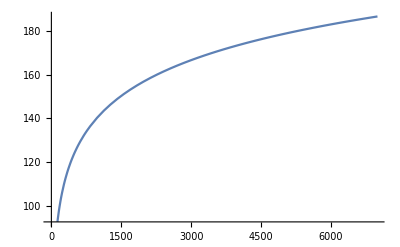

```mathematica
Plot[a,{z,-18.,7000}]
```

#### Coefficient “b”

```mathematica
b=1/(-0.2033682*Log[z])+0.0338898
```

0.0338898-4.91719/Log[z]

```mathematica
b=1/(-0.03723805*Log[z*669.8633])+1.330701
```

1.3307-26.8543/Log[669.863 z]

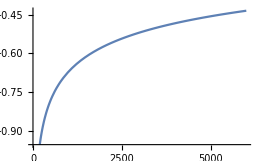

```mathematica
Plot[b,{z,0.,6000.}]
```

#### Where z is precipitation

## Harvest Output function

```mathematica
y = a x Exp[b x]
```

23.6716 ⅇ^(x (1.3307-26.8543/Log[669.863 z])) x Log[-22.7628+z]

#### Where x is LSU

## Plotting harvest output vs precipitation

```mathematica
Plot3D[y,{x,0,2},{z,0,6000}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
y/. {x-> 1.8,z-> 5699}
```

166.445